```mathematica
encrypt[n_,string_]:=(
encryption=RandomInteger[{1,500},{n,n}];
stringtrans=ToCharacterCode[string];
For[i=0,Mod[Length[stringtrans],n]≠ 0,i++,stringtrans=PadRight[ToCharacterCode[string],i+StringLength[string],32]];
stringtrans1=Transpose[Partition[stringtrans,n]];
estring=Transpose[Mod[encryption.(stringtrans1-32),97]+32];
estringtext=FromCharacterCode[Flatten[estring]]
)
decrypt[s_,msg_]:=(
stringtrans2=Transpose[Partition[ToCharacterCode[msg],s]];
{g,{a,b}}=ExtendedGCD[Abs[Det[encryption]],97];
dkey=Mod[Mod[a,97]*((Det[encryption]/Abs[Det[encryption]])*Det[encryption]*Inverse[encryption]),97];
txt=Transpose[Mod[dkey.(stringtrans2-32),97]+32];
FromCharacterCode[Flatten[txt]]
)
```

```mathematica
encrypt[15,"Hi, my name is Raymond Yuan. I am overachieving and a wrestler. :) "]
```

uVpdoXIuYu=dhWo$!ot1Y9P<&#\I2avyo#Q@0U$tR2.80a3RYRK7Uyv@.`AW%N^z%0XQ`89j|V&ON

```mathematica
decrypt[15,"uVpdoXIuYu=dhWo$!ot1Y9P<&#\\I2avyo#Q@0U$tR2.80a3RYRK7Uyv@.`AW%N^z%0XQ`89j|V&ON"]
```

Hi, my name is Raymond Yuan. I am overachieving and a wrestler. :)

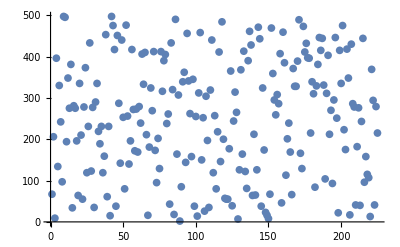

```mathematica
ListPlot[Flatten[encryption]]
```

```mathematica
encryption//MatrixForm
```

(67 | 206 | 9 | 396 | 134 | 330 | 242 | 97 | 497 | 495 | 194 | 348 | 275 | 381 | 34
281 | 275 | 196 | 64 | 335 | 210 | 55 | 278 | 373 | 119 | 231 | 433 | 123 | 277 | 35
290 | 335 | 219 | 189 | 231 | 119 | 159 | 453 | 61 | 231 | 15 | 497 | 475 | 417 | 38
451 | 287 | 142 | 440 | 253 | 80 | 476 | 256 | 140 | 196 | 417 | 272 | 172 | 273 | 169
279 | 239 | 406 | 333 | 410 | 211 | 16 | 181 | 324 | 269 | 412 | 173 | 95 | 202 | 129
412 | 316 | 390 | 405 | 238 | 261 | 43 | 433 | 320 | 18 | 490 | 164 | 307 | 2 | 85
339 | 362 | 144 | 456 | 341 | 262 | 158 | 345 | 38 | 255 | 14 | 312 | 458 | 150 | 252
26 | 304 | 197 | 35 | 319 | 440 | 119 | 257 | 80 | 218 | 411 | 146 | 484 | 200 | 57
55 | 55 | 177 | 365 | 39 | 244 | 314 | 265 | 7 | 126 | 368 | 164 | 413 | 122 | 81
390 | 461 | 428 | 64 | 212 | 65 | 126 | 471 | 443 | 38 | 324 | 174 | 23 | 16 | 8
67 | 469 | 359 | 295 | 259 | 308 | 286 | 407 | 46 | 459 | 385 | 113 | 201 | 239 | 169
66 | 371 | 328 | 328 | 389 | 489 | 166 | 129 | 473 | 411 | 432 | 397 | 396 | 215 | 339
310 | 84 | 329 | 381 | 446 | 415 | 444 | 331 | 104 | 311 | 403 | 212 | 270 | 93 | 295
446 | 251 | 22 | 415 | 335 | 475 | 223 | 175 | 418 | 348 | 17 | 430 | 286 | 278 | 41
182 | 276 | 40 | 243 | 444 | 96 | 158 | 115 | 107 | 13 | 369 | 294 | 41 | 279 | 215)

```mathematica
mariokey=Import["http://www.veryicon.com/icon/png/Game/Super%20Mario/Super%20Paper%20Mario.png"];
```

```mathematica
Rasterize[mariokey]
```

-Graphics-

```mathematica
256/3//N
```

85.3333

```mathematica
squarekey=(Cases[InputForm[Rasterize[mariokey]],Raster[___],Infinity][[1,1]]);
```

```mathematica
replaceskey=Table[(squarekey[[85+i,85+j]]),{i,0,14},{j,0,14}];
```

```mathematica
encryption[[1,1]]
```

67

```mathematica
Table[(ReplacePart[replaceskey,{1+i1,1+j1,3}->encryption[[i1,j1]]]),{i1,1,15,1},{j1,1,15,1}]
```

{{{{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14}},{{194,194,194},{0,0,67},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15}},12,{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}},13,{1}},14}
 |  |  |  |

```mathematica
Flatten[encryption][[1]]
```

67

```mathematica
ethree=Table[3n1,{n1,1,14,1}]
```

{3,6,9,12,15,18,21,24,27,30,33,36,39,42}

```mathematica
replaceskey1=Flatten[replaceskey];
Table[(replaceskey1[[3n1]]),{n1,1,75,1}]
```

{255,75,0,0,0,8,2,0,0,1,2,6,10,13,14,194,0,0,0,0,0,0,0,4,12,14,16,16,15,15,70,0,0,0,0,0,1,8,15,16,15,15,15,15,15,0,0,0,0,0,1,11,16,15,15,15,15,15,15,15,0,0,0,0,1,11,15,15,15,15,15,15,15,15,15}

```mathematica
225/3//N
```

75.

```mathematica
Partition[replaceskey1,3]
```

{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14},{194,194,194},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15},{70,70,70},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,1,1},{113,12,8},{207,22,15},{220,22,16},{211,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{26,5,1},{186,31,11},{227,26,16},{209,22,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{20,3,1},{200,34,11},{255,46,15},{222,30,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{67,12,4},{255,44,15},{245,43,14},{235,37,14},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{12,12,12},{0,0,0},{0,0,0},{0,0,0},{4,1,0},{200,35,12},{252,44,14},{243,42,14},{214,26,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{53,53,53},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{105,18,6},{255,45,15},{245,43,14},{227,33,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{64,64,64},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{24,4,1},{226,39,13},{249,43,14},{239,40,14},{209,22,15},{206,21,15},{207,21,15},{209,29,23},{207,21,15},{207,21,15},{47,47,47},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{143,25,8},{255,45,15},{245,43,14},{220,28,15},{205,20,15},{207,21,15},{207,22,16},{207,21,15},{207,21,15},{12,12,12},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{50,9,3},{243,42,14},{247,43,14},{233,36,14},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{178,31,10},{255,44,15},{242,42,14},{212,24,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{82,14,5},{254,44,15},{246,43,14},{225,32,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,2,0},{209,36,12},{252,44,14},{238,39,14},{208,21,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}

```mathematica
ReplacePart[Flatten[replaceskey],{ethree->67}]
```

{255,255,255,75,75,75,0,0,0,0,0,0,0,0,0,1,4,8,0,1,2,0,0,0,0,0,0,1,1,1,21,2,2,81,8,6,135,14,10,175,18,13,196,21,14,194,194,194,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,37,5,4,131,16,12,197,20,14,219,22,16,219,22,16,215,22,15,212,22,15,70,70,70,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,1,1,113,12,8,207,22,15,220,22,16,211,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,5,1,186,31,11,227,26,16,209,22,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,20,3,1,200,34,11,255,46,15,222,30,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,67,12,4,255,44,15,245,43,14,235,37,14,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,4,1,0,200,35,12,252,44,14,243,42,14,214,26,15,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,53,53,53,0,0,0,0,0,0,0,0,0,0,0,0,105,18,6,255,45,15,245,43,14,227,33,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,64,64,64,0,0,0,0,0,0,0,0,0,0,0,0,24,4,1,226,39,13,249,43,14,239,40,14,209,22,15,206,21,15,207,21,15,209,29,23,207,21,15,207,21,15,47,47,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,143,25,8,255,45,15,245,43,14,220,28,15,205,20,15,207,21,15,207,22,16,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50,9,3,243,42,14,247,43,14,233,36,14,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,178,31,10,255,44,15,242,42,14,212,24,15,206,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,82,14,5,254,44,15,246,43,14,225,32,15,205,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,2,0,209,36,12,252,44,14,238,39,14,208,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,118,20,6,255,45,15,244,43,14,217,27,15,205,20,15,207,21,15,207,21,15}

```mathematica
ReplacePart[Flatten[replaceskey],{3p_}->67]
```

{255,255,255,75,75,75,0,0,0,0,0,0,0,0,0,1,4,8,0,1,2,0,0,0,0,0,0,1,1,1,21,2,2,81,8,6,135,14,10,175,18,13,196,21,14,194,194,194,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,37,5,4,131,16,12,197,20,14,219,22,16,219,22,16,215,22,15,212,22,15,70,70,70,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,1,1,113,12,8,207,22,15,220,22,16,211,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,5,1,186,31,11,227,26,16,209,22,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,20,3,1,200,34,11,255,46,15,222,30,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,67,12,4,255,44,15,245,43,14,235,37,14,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,4,1,0,200,35,12,252,44,14,243,42,14,214,26,15,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,53,53,53,0,0,0,0,0,0,0,0,0,0,0,0,105,18,6,255,45,15,245,43,14,227,33,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,64,64,64,0,0,0,0,0,0,0,0,0,0,0,0,24,4,1,226,39,13,249,43,14,239,40,14,209,22,15,206,21,15,207,21,15,209,29,23,207,21,15,207,21,15,47,47,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,143,25,8,255,45,15,245,43,14,220,28,15,205,20,15,207,21,15,207,22,16,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50,9,3,243,42,14,247,43,14,233,36,14,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,178,31,10,255,44,15,242,42,14,212,24,15,206,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,82,14,5,254,44,15,246,43,14,225,32,15,205,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,2,0,209,36,12,252,44,14,238,39,14,208,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,118,20,6,255,45,15,244,43,14,217,27,15,205,20,15,207,21,15,207,21,15}

```mathematica
replaceskey
```

{{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14}},{{194,194,194},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15}},{{70,70,70},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,1,1},{113,12,8},{207,22,15},{220,22,16},{211,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{26,5,1},{186,31,11},{227,26,16},{209,22,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{20,3,1},{200,34,11},{255,46,15},{222,30,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{67,12,4},{255,44,15},{245,43,14},{235,37,14},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{4,1,0},{200,35,12},{252,44,14},{243,42,14},{214,26,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{53,53,53},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{105,18,6},{255,45,15},{245,43,14},{227,33,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{64,64,64},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{24,4,1},{226,39,13},{249,43,14},{239,40,14},{209,22,15},{206,21,15},{207,21,15},{209,29,23},{207,21,15},{207,21,15}},{{47,47,47},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{143,25,8},{255,45,15},{245,43,14},{220,28,15},{205,20,15},{207,21,15},{207,22,16},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{50,9,3},{243,42,14},{247,43,14},{233,36,14},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{178,31,10},{255,44,15},{242,42,14},{212,24,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{82,14,5},{254,44,15},{246,43,14},{225,32,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,2,0},{209,36,12},{252,44,14},{238,39,14},{208,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}}

```mathematica
Partition[(Cases[InputForm[-Graphics-],Point[___],Infinity][[1,1]])[[All,2]],15]//MatrixForm
```

(67. | 206. | 9. | 396. | 134. | 330. | 242. | 97. | 497. | 495. | 194. | 348. | 275. | 381. | 34.
281. | 275. | 196. | 64. | 335. | 210. | 55. | 278. | 373. | 119. | 231. | 433. | 123. | 277. | 35.
290. | 335. | 219. | 189. | 231. | 119. | 159. | 453. | 61. | 231. | 15. | 497. | 475. | 417. | 38.
451. | 287. | 142. | 440. | 253. | 80. | 476. | 256. | 140. | 196. | 417. | 272. | 172. | 273. | 169.
279. | 239. | 406. | 333. | 410. | 211. | 16. | 181. | 324. | 269. | 412. | 173. | 95. | 202. | 129.
412. | 316. | 390. | 405. | 238. | 261. | 43. | 433. | 320. | 18. | 490. | 164. | 307. | 2. | 85.
339. | 362. | 144. | 456. | 341. | 262. | 158. | 345. | 38. | 255. | 14. | 312. | 458. | 150. | 252.
26. | 304. | 197. | 35. | 319. | 440. | 119. | 257. | 80. | 218. | 411. | 146. | 484. | 200. | 57.
55. | 55. | 177. | 365. | 39. | 244. | 314. | 265. | 7. | 126. | 368. | 164. | 413. | 122. | 81.
390. | 461. | 428. | 64. | 212. | 65. | 126. | 471. | 443. | 38. | 324. | 174. | 23. | 16. | 8.
67. | 469. | 359. | 295. | 259. | 308. | 286. | 407. | 46. | 459. | 385. | 113. | 201. | 239. | 169.
66. | 371. | 328. | 328. | 389. | 489. | 166. | 129. | 473. | 411. | 432. | 397. | 396. | 215. | 339.
310. | 84. | 329. | 381. | 446. | 415. | 444. | 331. | 104. | 311. | 403. | 212. | 270. | 93. | 295.
446. | 251. | 22. | 415. | 335. | 475. | 223. | 175. | 418. | 348. | 17. | 430. | 286. | 278. | 41.
182. | 276. | 40. | 243. | 444. | 96. | 158. | 115. | 107. | 13. | 369. | 294. | 41. | 279. | 215.)

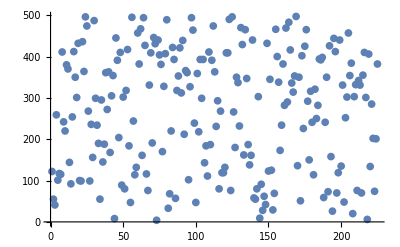
```mathematica
Cases[InputForm[-Graphics-],_Real]
```

{}

```mathematica
estring
```

{{86,44,61,123,115,118,112,37,56,55,100,64,73,112,94},{63,86,67,101,88,116,89,80,91,58,122,85,104,112,51},{100,53,34,58,100,86,101,57,124,106,113,102,46,48,78},{94,64,49,66,74,115,37,94,102,69,60,37,63,77,67},{94,126,101,125,89,113,44,120,86,93,63,58,57,53,118}}

```mathematica
estring//MatrixForm
```

(86 | 44 | 61 | 123 | 115 | 118 | 112 | 37 | 56 | 55 | 100 | 64 | 73 | 112 | 94
63 | 86 | 67 | 101 | 88 | 116 | 89 | 80 | 91 | 58 | 122 | 85 | 104 | 112 | 51
100 | 53 | 34 | 58 | 100 | 86 | 101 | 57 | 124 | 106 | 113 | 102 | 46 | 48 | 78
94 | 64 | 49 | 66 | 74 | 115 | 37 | 94 | 102 | 69 | 60 | 37 | 63 | 77 | 67
94 | 126 | 101 | 125 | 89 | 113 | 44 | 120 | 86 | 93 | 63 | 58 | 57 | 53 | 118)

```mathematica
Partition[ToCharacterCode["g/.:}.80yN"],4]//MatrixForm
```

(103 | 47 | 46 | 58
125 | 128 | 121 | 78)

```mathematica
stringtrans2//MatrixForm
```

(84 | 63 | 106 | 33 | 101
83 | 92 | 76 | 83 | 105
63 | 99 | 83 | 103 | 66
122 | 123 | 78 | 88 | 128
62 | 100 | 128 | 48 | 38
90 | 74 | 68 | 53 | 35
126 | 96 | 112 | 94 | 97
114 | 124 | 91 | 67 | 45
72 | 69 | 107 | 72 | 109
40 | 69 | 38 | 87 | 122
41 | 122 | 119 | 54 | 90
35 | 32 | 104 | 107 | 82
88 | 120 | 62 | 108 | 36
45 | 42 | 37 | 32 | 62
95 | 52 | 106 | 54 | 105)

```mathematica
stringtrans
```

{72,105,44,32,109,121,32,110,97,109,101,32,105,115,32,82,97,121,109,111,110,100,32,89,117,97,110,46,32,73,32,97,109,32,111,118,101,114,97,99,104,105,101,118,105,110,103,32,97,110,100,32,97,32,119,114,101,115,116,108,101,114,46,32,58,41,32,32,32,32,32,32,32,32,32}

```mathematica
Flatten[Transpose[Mod[dkey.(estring-32),97]+32]]
```

Dot::dotsh: Tensors « 1 » and {{54, 12, 29, 91, 83, 86, 80, 5, 24, 23, 68, 32, 41, 80, 62}, {31, 54, 35, 69, 56, 84, 57, 48, 59, 26, 90, 53, 72, 80, 19}, {68, 21, 2, 26, 68, 54, 69, 25, 92, 74, 81, 70, 14, 16, 46}, {62, 32, 17, 34, 42, 83, 5, 62, 70, 37, 28, 5, 31, 45, 35}, {62, 94, 69, 93, 57, 81, 12, 88, 54, 61, 31, 26, 25, 21, 86}} have incompatible shapes.

Transpose[32+Mod[{{54,85,15,56,15,6,25,27,70,68,73,14,18,16,87},{15,65,62,8,17,20,51,50,89,41,82,74,47,71,24},{52,81,81,72,5,41,68,71,17,52,79,57,57,16,36},{58,47,54,49,93,55,73,92,85,34,83,84,21,55,63},{0,69,73,78,76,40,20,23,44,25,76,81,83,53,7},{88,2,60,59,65,63,21,75,27,51,11,27,7,56,5},{16,19,88,9,30,8,67,29,68,26,37,40,69,26,70},{1,30,30,41,81,23,8,85,31,24,72,36,41,42,70},{52,10,4,32,17,26,13,68,7,34,79,16,69,24,11},{57,61,82,8,48,56,96,19,28,86,67,39,11,8,77},{43,91,55,93,80,66,18,44,38,11,11,22,50,30,89},{69,65,21,59,35,39,0,42,35,91,94,38,65,37,40},{6,41,42,36,38,31,7,58,31,80,77,13,82,27,82},{5,10,88,16,62,16,1,57,56,95,12,78,22,93,61},{49,83,44,25,51,53,66,86,28,96,13,36,79,88,23}}.{{54,12,29,91,83,86,80,5,24,23,68,32,41,80,62},{31,54,35,69,56,84,57,48,59,26,90,53,72,80,19},{68,21,2,26,68,54,69,25,92,74,81,70,14,16,46},{62,32,17,34,42,83,5,62,70,37,28,5,31,45,35},{62,94,69,93,57,81,12,88,54,61,31,26,25,21,86}},97]]

```mathematica
Transpose[Partition[ToCharacterCode["7TlT{EwZ"],4]]//MatrixForm
```

(55 | 123
84 | 69
108 | 119
84 | 90)

```mathematica
dkey//MatrixForm
```

(54 | 85 | 15 | 56 | 15 | 6 | 25 | 27 | 70 | 68 | 73 | 14 | 18 | 16 | 87
15 | 65 | 62 | 8 | 17 | 20 | 51 | 50 | 89 | 41 | 82 | 74 | 47 | 71 | 24
52 | 81 | 81 | 72 | 5 | 41 | 68 | 71 | 17 | 52 | 79 | 57 | 57 | 16 | 36
58 | 47 | 54 | 49 | 93 | 55 | 73 | 92 | 85 | 34 | 83 | 84 | 21 | 55 | 63
0 | 69 | 73 | 78 | 76 | 40 | 20 | 23 | 44 | 25 | 76 | 81 | 83 | 53 | 7
88 | 2 | 60 | 59 | 65 | 63 | 21 | 75 | 27 | 51 | 11 | 27 | 7 | 56 | 5
16 | 19 | 88 | 9 | 30 | 8 | 67 | 29 | 68 | 26 | 37 | 40 | 69 | 26 | 70
1 | 30 | 30 | 41 | 81 | 23 | 8 | 85 | 31 | 24 | 72 | 36 | 41 | 42 | 70
52 | 10 | 4 | 32 | 17 | 26 | 13 | 68 | 7 | 34 | 79 | 16 | 69 | 24 | 11
57 | 61 | 82 | 8 | 48 | 56 | 96 | 19 | 28 | 86 | 67 | 39 | 11 | 8 | 77
43 | 91 | 55 | 93 | 80 | 66 | 18 | 44 | 38 | 11 | 11 | 22 | 50 | 30 | 89
69 | 65 | 21 | 59 | 35 | 39 | 0 | 42 | 35 | 91 | 94 | 38 | 65 | 37 | 40
6 | 41 | 42 | 36 | 38 | 31 | 7 | 58 | 31 | 80 | 77 | 13 | 82 | 27 | 82
5 | 10 | 88 | 16 | 62 | 16 | 1 | 57 | 56 | 95 | 12 | 78 | 22 | 93 | 61
49 | 83 | 44 | 25 | 51 | 53 | 66 | 86 | 28 | 96 | 13 | 36 | 79 | 88 | 23)

```mathematica
a
```

40

```mathematica
encryption//MatrixForm
```

(332 | 433 | 404 | 454 | 189 | 199 | 91 | 284 | 231 | 153 | 296 | 370 | 247 | 207 | 215
248 | 71 | 245 | 459 | 318 | 161 | 437 | 367 | 261 | 463 | 139 | 352 | 279 | 100 | 160
441 | 473 | 22 | 242 | 326 | 319 | 151 | 165 | 353 | 47 | 467 | 18 | 355 | 226 | 302
213 | 190 | 119 | 344 | 97 | 395 | 485 | 88 | 246 | 315 | 461 | 253 | 450 | 383 | 80
452 | 55 | 356 | 269 | 462 | 478 | 390 | 44 | 33 | 429 | 373 | 373 | 360 | 11 | 183
292 | 392 | 426 | 255 | 157 | 239 | 465 | 399 | 95 | 423 | 465 | 105 | 385 | 69 | 320
379 | 365 | 165 | 190 | 161 | 291 | 393 | 45 | 91 | 132 | 166 | 93 | 202 | 384 | 356
493 | 431 | 46 | 178 | 356 | 332 | 379 | 33 | 12 | 49 | 384 | 362 | 41 | 485 | 341
387 | 361 | 397 | 463 | 175 | 376 | 224 | 437 | 92 | 262 | 343 | 374 | 426 | 157 | 423
346 | 180 | 185 | 440 | 108 | 223 | 373 | 421 | 33 | 387 | 22 | 90 | 375 | 193 | 113
216 | 366 | 52 | 470 | 239 | 471 | 409 | 299 | 471 | 201 | 145 | 41 | 9 | 150 | 12
181 | 241 | 231 | 65 | 50 | 216 | 94 | 44 | 170 | 243 | 471 | 352 | 497 | 79 | 179
2 | 284 | 97 | 372 | 451 | 365 | 361 | 46 | 28 | 214 | 88 | 340 | 419 | 212 | 79
331 | 406 | 475 | 312 | 20 | 93 | 459 | 388 | 481 | 355 | 165 | 171 | 286 | 429 | 314
113 | 451 | 14 | 495 | 486 | 75 | 68 | 385 | 114 | 215 | 375 | 108 | 382 | 406 | 498)

```mathematica
Mod[385,95]
```

5

```mathematica
estring//MatrixForm
```

(86 | 44 | 61 | 123 | 115 | 118 | 112 | 37 | 56 | 55 | 100 | 64 | 73 | 112 | 94
63 | 86 | 67 | 101 | 88 | 116 | 89 | 80 | 91 | 58 | 122 | 85 | 104 | 112 | 51
100 | 53 | 34 | 58 | 100 | 86 | 101 | 57 | 124 | 106 | 113 | 102 | 46 | 48 | 78
94 | 64 | 49 | 66 | 74 | 115 | 37 | 94 | 102 | 69 | 60 | 37 | 63 | 77 | 67
94 | 126 | 101 | 125 | 89 | 113 | 44 | 120 | 86 | 93 | 63 | 58 | 57 | 53 | 118)

```mathematica
Mod[{{79,48,34,28},
{32,64,67,73},
{41,33,35,90},
{84,92,16,9}}.(estring-32),95]+32
```

Dot::dotsh: Tensors {{79, 48, 34, 28}, {32, 64, 67, 73}, {41, 33, 35, 90}, {84, 92, 16, 9}} and {{54, 12, 29, 91, 83, 86, 80, 5, 24, 23, 68, 32, 41, 80, 62}, {31, 54, 35, 69, 56, 84, 57, 48, 59, 26, 90, 53, 72, 80, 19}, {68, 21, 2, 26, 68, 54, 69, 25, 92, 74, 81, 70, 14, 16, 46}, {62, 32, 17, 34, 42, 83, 5, 62, 70, 37, 28, 5, 31, 45, 35}, {62, 94, 69, 93, 57, 81, 12, 88, 54, 61, 31, 26, 25, 21, 86}} have incompatible shapes.

32+Mod[{{79,48,34,28},{32,64,67,73},{41,33,35,90},{84,92,16,9}}.{{54,12,29,91,83,86,80,5,24,23,68,32,41,80,62},{31,54,35,69,56,84,57,48,59,26,90,53,72,80,19},{68,21,2,26,68,54,69,25,92,74,81,70,14,16,46},{62,32,17,34,42,83,5,62,70,37,28,5,31,45,35},{62,94,69,93,57,81,12,88,54,61,31,26,25,21,86}},95]

```mathematica
encryption//MatrixForm
```

(332 | 433 | 404 | 454 | 189 | 199 | 91 | 284 | 231 | 153 | 296 | 370 | 247 | 207 | 215
248 | 71 | 245 | 459 | 318 | 161 | 437 | 367 | 261 | 463 | 139 | 352 | 279 | 100 | 160
441 | 473 | 22 | 242 | 326 | 319 | 151 | 165 | 353 | 47 | 467 | 18 | 355 | 226 | 302
213 | 190 | 119 | 344 | 97 | 395 | 485 | 88 | 246 | 315 | 461 | 253 | 450 | 383 | 80
452 | 55 | 356 | 269 | 462 | 478 | 390 | 44 | 33 | 429 | 373 | 373 | 360 | 11 | 183
292 | 392 | 426 | 255 | 157 | 239 | 465 | 399 | 95 | 423 | 465 | 105 | 385 | 69 | 320
379 | 365 | 165 | 190 | 161 | 291 | 393 | 45 | 91 | 132 | 166 | 93 | 202 | 384 | 356
493 | 431 | 46 | 178 | 356 | 332 | 379 | 33 | 12 | 49 | 384 | 362 | 41 | 485 | 341
387 | 361 | 397 | 463 | 175 | 376 | 224 | 437 | 92 | 262 | 343 | 374 | 426 | 157 | 423
346 | 180 | 185 | 440 | 108 | 223 | 373 | 421 | 33 | 387 | 22 | 90 | 375 | 193 | 113
216 | 366 | 52 | 470 | 239 | 471 | 409 | 299 | 471 | 201 | 145 | 41 | 9 | 150 | 12
181 | 241 | 231 | 65 | 50 | 216 | 94 | 44 | 170 | 243 | 471 | 352 | 497 | 79 | 179
2 | 284 | 97 | 372 | 451 | 365 | 361 | 46 | 28 | 214 | 88 | 340 | 419 | 212 | 79
331 | 406 | 475 | 312 | 20 | 93 | 459 | 388 | 481 | 355 | 165 | 171 | 286 | 429 | 314
113 | 451 | 14 | 495 | 486 | 75 | 68 | 385 | 114 | 215 | 375 | 108 | 382 | 406 | 498)

```mathematica
Det[encryption]
```

2198914398682305441462352113831333404360

```mathematica
Transpose[Table[((-1)^(q+w))*Minors[encryption,3][[q,w]],{q,4},{w,4}]]//MatrixForm
```

$Aborted

```mathematica
ExtendedGCD[121,26]
```

{1,{-3,14}}

```mathematica
Clear[a,b,g]
```

```mathematica
estringtext
```

z0osfW'j!z!+\.NJ#_0]GvZ3|^rQ

```mathematica
Det[encryption]
```

-1162616880

```mathematica
{g,{a,b}}=ExtendedGCD[Abs[Det[encryption]],97]
```

{1,{-32,383543713}}

```mathematica
Mod[a,95]
```

88

```mathematica
({{5, 8}, {17, 3}})
```

```mathematica
(Det[({{5, 8}, {17, 3}})]/Abs[Det[({{5, 8}, {17, 3}})]])
```

-1

```mathematica
(Det[({{5, 8}, {17, 3}})]/Abs[Det[({{5, 8}, {17, 3}})]])*Det[({{5, 8}, {17, 3}})]*Inverse[({{5, 8}, {17, 3}})]
```

{{-3,8},{17,-5}}

```mathematica
decrypt=Mod[Mod[a,97]*((Det[encryption]/Abs[Det[encryption]])*Det[encryption]*Inverse[encryption]),97]
```

{{50,2,46,4},{29,61,56,15},{68,29,20,52},{90,39,3,60}}

```mathematica
Mod[decrypt.(estring-32),97]+32
```

{{104,111},{101,32},{108,32},{108,32}}

```mathematica
stringtrans1
```

{{104,111},{101,32},{108,32},{108,32}}

```mathematica
encrypt[4,"hello"]
```

5*,Wh8zg

```mathematica
GCD[121,26]
```

1

```mathematica
Mod[121,26]
```

17

```mathematica
stringtrans1
```

{{104,111,121,109,115,121,100},{101,44,32,101,32,109,32},{108,32,110,32,114,111,32},{108,109,97,105,97,110,32}}

```mathematica
Mod[PowerMod[encryption,-1,89].(estring-32),95]+32
```

{{81,91,91,107,119,122,101},{58,116,100,78,73,126,98},{98,35,40,51,104,56,52},{117,80,39,125,122,51,90}}

```mathematica
encrypt[4,"hello, my name is raymond"]
```

?><%!_C(t*&>"TcA7dC3fu+8,k0#

```mathematica
stringtrans1//MatrixForm
```

(104 | 111 | 121 | 109 | 115 | 121 | 100
101 | 44 | 32 | 101 | 32 | 109 | 32
108 | 32 | 110 | 32 | 114 | 111 | 32
108 | 109 | 97 | 105 | 97 | 110 | 32)

```mathematica
stringtrans
```

{104,101,108,108,111,32,32,32}

```mathematica
estringtext
```

CP'cfEsk

```mathematica
encryption//MatrixForm
```

(13 | 26 | 297 | 369
465 | 210 | 449 | 324
468 | 451 | 195 | 130
482 | 300 | 411 | 38)

```mathematica
FromCharacterCode[Flatten[Mod[PowerMod[encryption,-1,89].(estring-32),95]]]
```

9.17]E&(.05X

```mathematica
ToCharacterCode["hello"]
```

{104,101,108,108,111}

```mathematica
stringtrans
```

{104,101,108,108,111,32,32,32}

```mathematica
estring
```

{{67,80},{39,99},{102,69},{115,107}}

```mathematica
FromCharacterCode[Flatten[PowerMod[encryption.(estring-32),-1,89]]]
```

.08.016.07Q\r.136

```mathematica
stringtrans1//MatrixForm
estring
estringtext
stringtrans2//MatrixForm
```

(104 | 111
101 | 32
108 | 32
108 | 32)

{{67,80},{39,99},{102,69},{115,107}}

CP'cfEsk

(1119274563791/9279143799 | 1122245895523/9279143799
301197280187/9279143799 | 297517888174/9279143799
99986902409/3093047933 | 99618099875/3093047933
1121042158147/9279143799 | 1122414160334/9279143799)

```mathematica
Inverse[encryption].encryption.stringtrans1
```

{{104,111},{101,32},{108,32},{108,32}}

```mathematica
encrypt[4,"hello."]
```

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 65536, is expected at position 1 in {454831111/13957063, 449524606/13957063, 1685138114/13957063, 447001071/13957063, 1685306755/13957063, 1688084156/13957063, 448556475/13957063, 1688326824/13957063}.

FromCharacterCode[{454831111/13957063,449524606/13957063,1685138114/13957063,447001071/13957063,1685306755/13957063,1688084156/13957063,448556475/13957063,1688326824/13957063}]

```mathematica
estring//MatrixForm
```

(43 | 39
107 | 105
79 | 73
95 | 62)

```mathematica
256
```

256